```mathematica
Assuming[t>1, ∫_1^t x^(-3/2)ⅆx]
```

2-2/(√t)

```mathematica
Limit[%, t->∞]
```

2

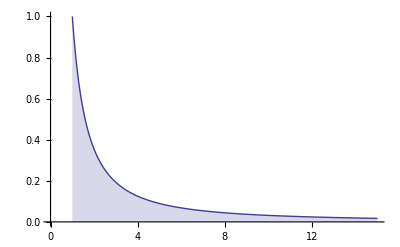

```mathematica
Plot[x^(-3/2), {x,1,15}, PlotRange->{{0,15}, All}, Filling->Axis]
```

```mathematica
Assuming[0<t<1, ∫_t^1 1/√(e^x - 1)ⅆx]
```

(2 (ArcTan[√(-1+e)]-ArcTan[√(-1+e^t)]))/Log[e]

```mathematica
Limit[%, t->0, Direction->-1]
```

(2 ArcTan[√(-1+e)])/Log[e]

```mathematica
Limit[%, t->0, Direction->-1]
%//N
```

(2 ArcTan[√(-1+e)])/Log[e]

(2. ArcTan[√(-1.+e)])/Log[e]

```mathematica
%//N
```

(2. ArcTan[√(-1.+e)])/Log[e]

```mathematica
Plot[1/√((e^x )- 1), {x,0,1}, PlotRange->{0,8}, Filling->Axis]
```

Plot::exclul: {Im[e] - 0, Im[e^x] - 0} must be a list of equalities or real-valued functions.

```mathematica
-Graphics-

Plot[1/√((e^x )- 1), {x,0,1}, PlotRange->{0,8}, Filling->Axis]
```

-Graphics-

Plot::exclul: {Im[e] - 0, Im[e^x] - 0} must be a list of equalities or real-valued functions.

-Graphics-

```mathematica
Plot[1/sqrt ( e^x - 1), {x,0,1}, PlotRange->{0,8}, Filling->Axis]
```

Plot::exclul: {Im[e] - 0} must be a list of equalities or real-valued functions.

-Graphics-

```mathematica
Assuming[0<t<π/2, ∫_0^t Tan[x]ⅆx]
```

-Log[Cos[t]]

```mathematica
Limit[%, t-> π/2]
```

∞

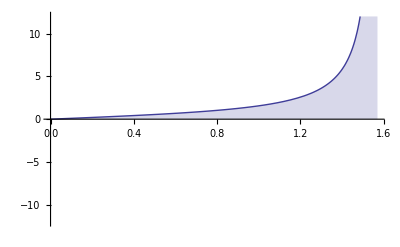

```mathematica
Plot[Tan[x],{x,0,π/2},Filling->Axis, PlotRange->{-12,12}]
```

```mathematica
Plot[1/ √(√x(1-√x)), {x,0,1}, PlotRange->{0,10}, Filling->Axis]
```

Plot::nonopt: Options expected (instead of Filling - Axis) beyond position 2 in Plot[1/√√x (1 - Power[« 2 »]), {x, 0, 1}, PlotRange → {0, 10}, Filling - Axis]. An option must be a rule or a list of rules.

Plot[1/(√(√x (1-√x))),{x,0,1},PlotRange→{0,10},Filling-Axis]

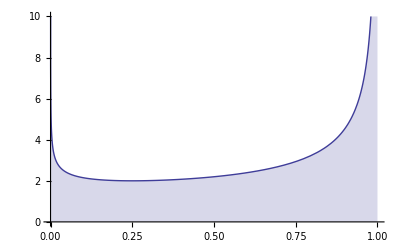

```mathematica
Plot[1/ √(√x(1-√x)), {x,0,1}, PlotRange->{0,10}, Filling->Axis]
```

```mathematica
∫1/ √(√x(1-√x))ⅆx
```

-2 √(√x-x)-ArcSin[1-2 √x]

```mathematica
Limit[%, x->1, Direction->1] - Limit[%, x->0, Direction->-1]
```

0

```mathematica
∫1/ √(√x(1-√x))ⅆx
Limit[%, x->1, Direction->1] - Limit[%, x->0, Direction->-1]
```

-2 √(√x-x)-ArcSin[1-2 √x]

π